```mathematica
SetDirectory["C:\\Users\\benja\\OneDrive\\Documents\\GitHub\\KhovanovLaplacian\\basic_khovanov_testing"]
<< KnotTheory`
<< KhovanovLaplacian`
```

C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing

ParentDirectory::nums: Argument File should be a positive machine-size integer, a nonempty string, or a File specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{File,WikiLink,mathematica}].

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{File,QuantumGroups}].

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Loading KhovanovLaplacian`...

q::shdw: Symbol q appears in multiple contexts {KhovanovLaplacian`,Global`}; definitions in context KhovanovLaplacian` may shadow or be shadowed by other definitions.

t::shdw: Symbol t appears in multiple contexts {KhovanovLaplacian`,Global`}; definitions in context KhovanovLaplacian` may shadow or be shadowed by other definitions.

```mathematica
PD[Knot[8,12]]
```

PD[X[4,2,5,1],X[10,8,11,7],X[8,3,9,4],X[2,9,3,10],X[14,6,15,5],X[16,11,1,12],X[12,15,13,16],X[6,14,7,13]]

```mathematica
qSpectraAllEigs[PD[Knot[8,12]]]
```

Get::path: ParentDirectory[File] in $Path is not a string.

KnotTheory::loading: Loading precomputed data in PD4Knots`.

qSpectraAllEigs[-4,-9] = {0.}

qSpectraAllEigs[-4,-7] = {6.92542,4.55193,2.61803,1.52265,0.381966}

qSpectraAllEigs[-4,-5] = {11.4409,8.09441,7.30278,6.70996,6.23607,4.73725,4.23688,3.69722,1.78063,1.76393}

qSpectraAllEigs[-4,-3] = {12.7654,10.0096,8.79854,8.59286,7.38554,6.09944,5.84756,5.49883,4.17404,2.82824}

qSpectraAllEigs[-4,-1] = {11.3429,9.47068,7.18639,7.,5.}

qSpectraAllEigs[-4,1] = {8.}

qSpectraAllEigs[-3,-7] = {6.92542,4.55193,2.61803,2.,2.,1.52265,0.381966,-1.2802×10^-15}

qSpectraAllEigs[-3,-5] = {11.4409,11.1534,10.2516,9.91041,9.51882,9.46896,9.2956,9.05137,8.09441,7.30278,6.70996,6.3907,6.23607,6.0743,5.75088,5.4827,4.73725,4.23688,4.1844,4.17176,4.,3.69722,3.46593,3.27803,3.09048,3.,2.56621,2.40732,1.78063,1.76393,1.4871,6.31353×10^-15}

qSpectraAllEigs[-3,-3] = {13.8968,13.8513,13.2952,12.8268,12.7654,12.6412,12.4107,12.2971,10.5775,10.2035,10.1287,10.0096,9.7868,9.69979,9.41739,9.31095,9.,8.79854,8.59286,8.55037,8.2507,8.,7.38554,7.22962,7.05412,7.,6.80518,6.09944,5.99539,5.91613,5.88774,5.84756,5.67997,5.58866,5.49883,5.27129,5.14281,5.,4.89511,4.52973,4.43382,4.34558,4.17404,4.,3.53788,2.82824,2.53907,1.0032}

qSpectraAllEigs[-3,-1] = {13.0514,12.8027,12.64,12.4757,12.4086,12.3037,11.8479,11.3429,10.8646,9.94108,9.79322,9.4827,9.47068,9.19578,8.41061,8.07062,8.,8.,7.54249,7.46593,7.30469,7.18639,7.,6.63463,6.49534,6.27561,5.82396,5.67605,5.,5.,4.83961,3.653}

qSpectraAllEigs[-3,1] = {10.,10.,8.,8.,8.,8.,8.,8.}

qSpectraAllEigs[-2,-7] = {2.,2.}

qSpectraAllEigs[-2,-5] = {11.1534,10.2516,9.91041,9.51882,9.46896,9.2956,9.05137,8.82843,8.37228,6.3907,6.0743,6.,5.75088,5.4827,4.1844,4.17176,4.,4.,4.,4.,4.,4.,3.46593,3.27803,3.17157,3.09048,3.,3.,2.62772,2.56621,2.40732,2.,1.4871,-1.41307×10^-15,-1.07195×10^-15,4.9371×10^-16}

qSpectraAllEigs[-2,-3] = {14.,13.8968,13.8513,13.7315,13.6828,13.5163,13.4907,13.4313,13.2952,13.1487,12.8589,12.8268,12.7087,12.6489,12.6484,12.6412,12.4107,12.4086,12.3313,12.2971,12.,11.945,11.7588,11.7523,11.5967,11.3481,11.,11.,10.5775,10.2035,10.1287,9.9239,9.7868,9.69979,9.41739,9.31095,9.,8.97599,8.55037,8.53702,8.2507,8.,8.,8.,7.98032,7.6185,7.30541,7.22962,7.05412,7.03584,7.,6.80518,6.64838,6.54385,6.30438,5.99539,5.91613,5.88774,5.67997,5.63587,5.58866,5.49901,5.32332,5.27129,5.16009,5.14281,5.,5.,5.,5.,4.93582,4.89511,4.85346,4.81057,4.80178,4.66873,4.56767,4.52973,4.46353,4.43382,4.35156,4.34558,4.04277,4.,3.89878,3.8112,3.53788,3.31716,2.76028,2.53907,2.14382,2.02103,1.6241,1.09824,1.0032,0.802638,0.527939,-1.03482×10^-14}

qSpectraAllEigs[-2,-1] = {14.4219,14.4071,14.3837,14.3817,14.3381,14.3166,14.3166,14.0671,14.0132,13.8815,13.7996,13.7293,13.7267,13.6235,13.6039,13.4941,13.3945,13.0514,13.0066,12.9864,12.8027,12.6964,12.64,12.5215,12.4757,12.4086,12.3037,11.8479,10.9325,10.8901,10.8646,10.82,10.507,10.459,10.0759,10.,10.,10.,9.94108,9.92266,9.84128,9.83296,9.79322,9.4827,9.25105,9.19578,9.12693,8.95764,8.63146,8.60901,8.41061,8.32848,8.07062,8.,8.,8.,7.71551,7.68338,7.68338,7.54249,7.50604,7.48486,7.46593,7.34798,7.30469,7.19461,6.98869,6.63463,6.56802,6.49534,6.42678,6.27561,6.23987,6.21471,6.15214,5.97915,5.82396,5.78864,5.67605,5.6748,5.65832,5.46483,5.,4.83961,4.79163,4.78567,4.50441,3.9121,3.75953,3.653,3.56801,3.45412,3.16215,2.7082,2.67079,2.27275,1.91405,1.42883}

qSpectraAllEigs[-2,1] = {12.,12.,12.,11.4937,11.1623,10.7718,10.3166,10.3166,10.,10.,10.,10.,10.,10.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.5099,6.3758,6.,4.83772,3.84876,3.68338,3.68338}

qSpectraAllEigs[-2,3] = {6.,6.}

qSpectraAllEigs[-1,-5] = {8.82843,8.37228,6.,4.,4.,4.,4.,4.,4.,4.,3.17157,3.,2.62772,2.}

qSpectraAllEigs[-1,-3] = {14.,13.7315,13.6828,13.5163,13.4907,13.4313,13.1487,12.8589,12.7087,12.6489,12.6484,12.4086,12.3313,12.,12.,12.,11.945,11.7588,11.7523,11.7016,11.5967,11.4824,11.4641,11.4641,11.3723,11.3481,11.,11.,10.8284,10.4609,10.0888,9.9239,9.70356,9.56155,8.97599,8.53702,8.,8.,7.98032,7.6185,7.35477,7.30541,7.13654,7.03584,6.64838,6.54385,6.30438,6.,6.,6.,6.,6.,6.,6.,5.9362,5.63587,5.62772,5.49901,5.43845,5.32332,5.29844,5.17157,5.16009,5.,5.,5.,5.,5.,5.,4.93582,4.85346,4.81057,4.80668,4.80178,4.66873,4.56767,4.5359,4.5359,4.46353,4.35156,4.04277,4.,3.89878,3.8112,3.31716,3.02379,2.76028,2.39415,2.14382,2.02103,1.89291,1.71924,1.6241,1.09824,0.802638,0.527939,4.3299×10^-15,3.55268×10^-15}

Eigenvalues::arh: Because finding 168 out of the 168 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

qSpectraAllEigs[-1,-1] = …

qSpectraAllEigs[-1,1] = {14.,14.,14.,14.,14.,14.,13.635,13.1661,13.1251,13.1056,13.052,13.0347,12.9796,12.8726,12.4495,12.4244,12.3112,12.2799,12.1206,12.,12.,12.,12.,12.,11.9554,11.8927,11.4937,11.3899,11.1623,11.0265,10.7718,10.5419,10.4346,10.4201,10.3166,10.3166,10.,10.,10.,10.,10.,10.,9.24797,8.91136,8.742,8.60741,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.59967,7.55051,7.54689,7.5099,7.37506,7.33887,7.31665,7.30936,6.82907,6.55468,6.3758,6.33589,6.17798,6.16631,6.10151,6.,5.41159,5.40898,4.83772,4.83169,4.67973,4.53984,4.52223,3.84876,3.68338,3.68338,3.66529,3.66514,3.61052,3.,2.77883,2.57557,2.02693,1.68299,1.67212}

qSpectraAllEigs[-1,3] = {9.56155,8.,8.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.43845,5.}

qSpectraAllEigs[0,-5] = {4.,4.}

qSpectraAllEigs[0,-3] = {12.,12.,11.7016,11.4824,11.4641,11.4641,11.3723,10.8284,10.4609,10.0888,10.,9.70356,9.56155,9.56155,7.35477,7.13654,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.9362,5.62772,5.43845,5.43845,5.29844,5.17157,5.,5.,5.,5.,4.80668,4.5359,4.5359,4.,3.02379,2.39415,1.89291,1.71924}

Eigenvalues::arh: Because finding 166 out of the 166 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

qSpectraAllEigs[0,-1] = …

Eigenvalues::arh: Because finding 166 out of the 166 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

qSpectraAllEigs[0,1] = …

qSpectraAllEigs[0,3] = {12.,11.578,11.5616,11.4641,11.4641,10.8284,10.3694,10.,10.,9.87162,9.56155,9.56155,9.06515,8.,8.,8.,7.43845,7.,6.35044,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.47113,5.43845,5.43845,5.37714,5.17157,5.12562,5.,5.,4.84377,4.5359,4.5359,4.,3.90299,3.28782,1.53163,1.22526}

qSpectraAllEigs[0,5] = {4.,4.}

qSpectraAllEigs[1,-3] = {10.,9.56155,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.43845,5.}

qSpectraAllEigs[1,-1] = {14.,14.,14.,14.,14.,14.,13.6435,13.4924,13.3556,13.2144,13.1871,13.0853,12.9969,12.8778,12.876,12.7416,12.5919,12.5441,12.3577,12.2424,12.1113,12.,12.,12.,12.,12.,11.666,11.6219,11.3922,11.1214,11.0349,11.0093,10.5974,10.5516,10.4495,10.4439,10.4433,10.393,10.,10.,10.,10.,9.65321,9.48739,8.555,8.40044,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.91148,7.76641,7.66944,7.58921,7.50779,7.37482,7.3503,7.34244,7.31438,6.90794,6.90114,6.,5.83739,5.62369,5.57329,5.55051,5.29169,5.2453,4.68168,4.67936,4.58255,4.35478,4.20902,4.20566,4.18288,4.15625,4.00795,3.95677,3.85818,3.65595,3.55413,3.37675,2.99355,2.76238,2.0778,1.95832,1.85061}

qSpectraAllEigs[1,1] = …

qSpectraAllEigs[1,3] = {14.,13.7315,13.6828,13.5163,13.5051,13.4847,13.4313,13.1602,13.1231,12.7975,12.785,12.6484,12.5833,12.4086,12.3313,12.1101,12.1101,12.,12.,11.8585,11.7914,11.578,11.5616,11.4693,11.4641,11.4641,10.8284,10.3694,10.,10.,9.87162,9.56155,9.18721,9.06756,9.06515,8.76308,8.,7.65218,7.60234,7.43845,7.31666,7.06921,7.,6.51972,6.51972,6.35044,6.04406,6.,6.,6.,6.,6.,6.,6.,6.,5.79736,5.54058,5.47113,5.43845,5.37714,5.37019,5.37019,5.17157,5.16009,5.14601,5.12562,5.03665,5.,5.,4.89962,4.87689,4.85346,4.84377,4.66873,4.61777,4.5359,4.5359,4.51853,4.45572,4.35156,4.,3.90299,3.89976,3.89878,3.31716,3.28782,3.20855,2.84027,2.44711,1.99651,1.58955,1.53163,1.39637,1.22526,0.995133,0.477043,-1.34337×10^-14,-7.10542×10^-15}

qSpectraAllEigs[1,5] = {8.82843,7.56155,6.,4.,4.,4.,4.,4.,4.,4.,3.43845,3.17157,3.,2.}

qSpectraAllEigs[2,-3] = {6.,6.}

qSpectraAllEigs[2,-1] = {12.,12.,12.,11.666,11.6219,11.0093,10.4495,10.4439,10.4433,10.,10.,10.,10.,10.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.66944,7.3503,5.55051,5.2453,4.68168,4.35478,3.85818,3.65595}

qSpectraAllEigs[2,1] = {14.5195,14.4713,14.3906,14.3088,14.1507,14.0226,13.9433,13.917,13.8004,13.8004,13.78,13.7266,13.6929,13.5882,13.5796,13.4641,13.423,13.3973,13.1878,13.0291,12.9919,12.7326,12.6728,12.5679,12.5509,12.3209,12.2691,12.1446,12.,11.3097,11.0917,11.0917,11.0618,10.7026,10.4119,10.3493,10.3395,10.246,10.0804,10.0612,10.,9.79914,9.42188,9.37346,9.16414,9.06519,9.06127,8.82381,8.76565,8.64806,8.59199,8.48906,8.31542,8.3098,8.25676,8.12554,8.12054,7.97016,7.86153,7.71012,7.41396,7.10781,7.10781,7.01488,6.86957,6.82211,6.67912,6.57808,6.5359,6.50718,6.35758,6.32937,6.18633,6.17793,6.04319,5.95497,5.79284,5.3604,5.31759,5.17646,5.07655,5.05116,4.89148,4.70459,4.64786,4.52366,4.38742,4.12573,3.73053,3.58691,3.41568,3.06667,3.02997,2.70689,2.5354,2.32931,1.91412,1.87957}

qSpectraAllEigs[2,3] = {14.,13.7315,13.6828,13.5163,13.5051,13.4847,13.4313,13.2747,13.2576,13.1602,13.1231,12.8662,12.7975,12.785,12.7059,12.6484,12.5833,12.4265,12.4086,12.4085,12.3766,12.3313,12.1101,12.1101,12.,11.8585,11.7914,11.4693,11.4446,10.6819,10.6407,10.4784,10.2361,9.9834,9.91549,9.60077,9.18721,9.06756,8.76308,8.71836,8.63346,8.03448,7.65218,7.60234,7.41897,7.31666,7.06921,6.72737,6.51972,6.51972,6.29018,6.04406,6.,6.,5.97965,5.79736,5.76393,5.70959,5.54058,5.37662,5.37019,5.37019,5.29575,5.16009,5.14601,5.05729,5.03665,5.,4.9276,4.92365,4.89962,4.87689,4.85515,4.85346,4.66873,4.61777,4.60649,4.51853,4.45572,4.35156,4.31164,4.15695,3.97202,3.89976,3.89878,3.31716,3.27034,3.20855,2.84027,2.52747,2.44711,1.99651,1.58955,1.39637,1.14576,0.995133,0.477043,7.10543×10^-15}

qSpectraAllEigs[2,5] = {11.3568,10.616,10.6056,10.1935,10.0624,9.88448,9.41344,8.82843,7.56155,6.,5.09236,5.,4.88425,4.61393,4.43188,4.,4.,4.,4.,4.,4.,3.86143,3.43845,3.39445,3.38079,3.23127,3.17157,3.,3.,2.84584,2.66411,2.,1.46758,-4.79354×10^-15,-2.96865×10^-15,-2.10091×10^-15}

qSpectraAllEigs[2,7] = {2.,2.}

qSpectraAllEigs[3,-1] = {10.,10.,8.,8.,8.,8.,8.,8.}

qSpectraAllEigs[3,1] = {13.0291,12.7326,12.6728,12.5679,12.5509,12.3209,12.1446,11.5456,10.4119,10.,9.42188,9.06519,9.06127,8.64806,8.62306,8.48906,8.25676,8.12054,8.,7.97016,7.71012,7.,6.86957,6.67912,6.50718,6.35758,5.95497,5.31759,5.07655,4.83133,4.64786,3.41568}

qSpectraAllEigs[3,3] = {13.2747,13.2576,12.8662,12.7059,12.4265,12.4085,12.3947,12.3766,11.4446,10.6819,10.6407,10.4784,10.2665,10.2361,9.9834,9.91549,9.60077,9.32796,8.71836,8.63346,8.12556,8.03448,7.48793,7.41897,6.72737,6.55165,6.29018,6.,5.97965,5.76393,5.70959,5.70793,5.37662,5.36047,5.29575,5.05729,4.9276,4.92365,4.85515,4.60649,4.31164,4.15695,3.97202,3.96347,3.27034,2.81383,2.52747,1.14576}

qSpectraAllEigs[3,5] = {11.3568,11.2306,10.616,10.6056,10.1935,10.0624,9.88448,9.41344,8.70555,7.87837,6.92895,5.10639,5.09236,5.,4.88425,4.61499,4.61393,4.43188,4.23879,4.,3.86143,3.82604,3.39445,3.38079,3.23127,3.,2.84584,2.66411,1.79332,1.67699,1.46758,5.70486×10^-16}

qSpectraAllEigs[3,7] = {7.63299,3.70347,2.76511,2.,2.,1.48486,0.41356,1.00094×10^-15}

qSpectraAllEigs[4,-1] = {8.}

qSpectraAllEigs[4,1] = {11.5456,8.62306,8.,7.,4.83133}

qSpectraAllEigs[4,3] = {12.3947,10.2665,9.32796,8.12556,7.48793,6.55165,5.70793,5.36047,3.96347,2.81383}

qSpectraAllEigs[4,5] = {11.2306,8.70555,7.87837,6.92895,5.10639,4.61499,4.23879,3.82604,1.79332,1.67699}

qSpectraAllEigs[4,7] = {7.63299,3.70347,2.76511,1.48486,0.41356}

qSpectraAllEigs[4,9] = {0.}

{{{0.},{6.92542,4.55193,2.61803,1.52265,0.381966},{11.4409,8.09441,7.30278,6.70996,6.23607,4.73725,4.23688,3.69722,1.78063,1.76393},{12.7654,10.0096,8.79854,8.59286,7.38554,6.09944,5.84756,5.49883,4.17404,2.82824},{11.3429,9.47068,7.18639,7.,5.},{8.}},{{6.92542,4.55193,2.61803,2.,2.,1.52265,0.381966,-1.2802×10^-15},{11.4409,11.1534,10.2516,9.91041,9.51882,9.46896,9.2956,9.05137,8.09441,7.30278,6.70996,6.3907,6.23607,6.0743,5.75088,5.4827,4.73725,4.23688,4.1844,4.17176,4.,3.69722,3.46593,3.27803,3.09048,3.,2.56621,2.40732,1.78063,1.76393,1.4871,6.31353×10^-15},{13.8968,13.8513,13.2952,12.8268,12.7654,12.6412,12.4107,12.2971,10.5775,10.2035,10.1287,10.0096,9.7868,9.69979,9.41739,9.31095,9.,8.79854,8.59286,8.55037,8.2507,8.,7.38554,7.22962,7.05412,7.,6.80518,6.09944,5.99539,5.91613,5.88774,5.84756,5.67997,5.58866,5.49883,5.27129,5.14281,5.,4.89511,4.52973,4.43382,4.34558,4.17404,4.,3.53788,2.82824,2.53907,1.0032},{13.0514,12.8027,12.64,12.4757,12.4086,12.3037,11.8479,11.3429,10.8646,9.94108,9.79322,9.4827,9.47068,9.19578,8.41061,8.07062,8.,8.,7.54249,7.46593,7.30469,7.18639,7.,6.63463,6.49534,6.27561,5.82396,5.67605,5.,5.,4.83961,3.653},{10.,10.,8.,8.,8.,8.,8.,8.}},{{2.,2.},{11.1534,10.2516,9.91041,9.51882,9.46896,9.2956,9.05137,8.82843,8.37228,6.3907,6.0743,6.,5.75088,5.4827,4.1844,4.17176,4.,4.,4.,4.,4.,4.,3.46593,3.27803,3.17157,3.09048,3.,3.,2.62772,2.56621,2.40732,2.,1.4871,-1.41307×10^-15,-1.07195×10^-15,4.9371×10^-16},{14.,13.8968,13.8513,13.7315,13.6828,13.5163,13.4907,13.4313,13.2952,13.1487,12.8589,12.8268,12.7087,12.6489,12.6484,12.6412,12.4107,12.4086,12.3313,12.2971,12.,11.945,11.7588,11.7523,11.5967,11.3481,11.,11.,10.5775,10.2035,10.1287,9.9239,9.7868,9.69979,9.41739,9.31095,9.,8.97599,8.55037,8.53702,8.2507,8.,8.,8.,7.98032,7.6185,7.30541,7.22962,7.05412,7.03584,7.,6.80518,6.64838,6.54385,6.30438,5.99539,5.91613,5.88774,5.67997,5.63587,5.58866,5.49901,5.32332,5.27129,5.16009,5.14281,5.,5.,5.,5.,4.93582,4.89511,4.85346,4.81057,4.80178,4.66873,4.56767,4.52973,4.46353,4.43382,4.35156,4.34558,4.04277,4.,3.89878,3.8112,3.53788,3.31716,2.76028,2.53907,2.14382,2.02103,1.6241,1.09824,1.0032,0.802638,0.527939,-1.03482×10^-14},{14.4219,14.4071,14.3837,14.3817,14.3381,14.3166,14.3166,14.0671,14.0132,13.8815,13.7996,13.7293,13.7267,13.6235,13.6039,13.4941,13.3945,13.0514,13.0066,12.9864,12.8027,12.6964,12.64,12.5215,12.4757,12.4086,12.3037,11.8479,10.9325,10.8901,10.8646,10.82,10.507,10.459,10.0759,10.,10.,10.,9.94108,9.92266,9.84128,9.83296,9.79322,9.4827,9.25105,9.19578,9.12693,8.95764,8.63146,8.60901,8.41061,8.32848,8.07062,8.,8.,8.,7.71551,7.68338,7.68338,7.54249,7.50604,7.48486,7.46593,7.34798,7.30469,7.19461,6.98869,6.63463,6.56802,6.49534,6.42678,6.27561,6.23987,6.21471,6.15214,5.97915,5.82396,5.78864,5.67605,5.6748,5.65832,5.46483,5.,4.83961,4.79163,4.78567,4.50441,3.9121,3.75953,3.653,3.56801,3.45412,3.16215,2.7082,2.67079,2.27275,1.91405,1.42883},{12.,12.,12.,11.4937,11.1623,10.7718,10.3166,10.3166,10.,10.,10.,10.,10.,10.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.5099,6.3758,6.,4.83772,3.84876,3.68338,3.68338},{6.,6.}},{{8.82843,8.37228,6.,4.,4.,4.,4.,4.,4.,4.,3.17157,3.,2.62772,2.},{14.,13.7315,13.6828,13.5163,13.4907,13.4313,13.1487,12.8589,12.7087,12.6489,12.6484,12.4086,12.3313,12.,12.,12.,11.945,11.7588,11.7523,11.7016,11.5967,11.4824,11.4641,11.4641,11.3723,11.3481,11.,11.,10.8284,10.4609,10.0888,9.9239,9.70356,9.56155,8.97599,8.53702,8.,8.,7.98032,7.6185,7.35477,7.30541,7.13654,7.03584,6.64838,6.54385,6.30438,6.,6.,6.,6.,6.,6.,6.,5.9362,5.63587,5.62772,5.49901,5.43845,5.32332,5.29844,5.17157,5.16009,5.,5.,5.,5.,5.,5.,4.93582,4.85346,4.81057,4.80668,4.80178,4.66873,4.56767,4.5359,4.5359,4.46353,4.35156,4.04277,4.,3.89878,3.8112,3.31716,3.02379,2.76028,2.39415,2.14382,2.02103,1.89291,1.71924,1.6241,1.09824,0.802638,0.527939,4.3299×10^-15,3.55268×10^-15},{16.,16.,16.,16.,16.,16.,15.4851,15.4613,15.4384,15.3945,15.37,15.2658,14.9479,14.9427,14.8434,14.7333,14.7276,14.6056,14.6056,14.6056,14.6056,14.4219,14.4071,14.3837,14.3817,14.3381,14.3166,14.3166,14.0671,14.0132,13.9244,13.8815,13.7996,13.7444,13.7293,13.7267,13.6235,13.6039,13.5675,13.5223,13.4941,13.421,13.3945,13.2361,13.2361,13.1334,13.0363,13.0066,12.9864,12.9819,12.974,12.8636,12.7888,12.7231,12.6964,12.5215,11.7552,11.7485,11.6587,11.6004,11.1524,10.9727,10.9325,10.9124,10.8901,10.82,10.507,10.459,10.3664,10.2086,10.0759,10.0151,10.,10.,10.,9.92266,9.84128,9.83296,9.57631,9.25105,9.22431,9.12693,9.00553,8.95764,8.89454,8.76393,8.76393,8.71437,8.64811,8.63146,8.60901,8.55817,8.34158,8.32848,8.01282,8.,7.71551,7.68338,7.68338,7.52591,7.50604,7.48486,7.39445,7.39445,7.39445,7.39445,7.38358,7.34798,7.19461,7.07283,7.04971,6.98869,6.84699,6.82321,6.77563,6.63096,6.56802,6.45049,6.42678,6.23987,6.21471,6.16254,6.15214,6.10192,6.02992,5.97915,5.78864,5.6748,5.65832,5.53226,5.46483,4.9893,4.89446,4.79163,4.78567,4.50441,4.42165,4.3709,4.36979,4.2329,4.15501,3.91286,3.9121,3.8631,3.75953,3.56801,3.45707,3.45412,3.17469,3.16215,2.93146,2.75258,2.7082,2.67079,2.61879,2.50941,2.27275,2.2175,2.11197,1.98697,1.91405,1.68877,1.42883,1.18105,1.11694,-4.36578×10^-15,4.02658×10^-15,1.70946×10^-15},{14.,14.,14.,14.,14.,14.,13.635,13.1661,13.1251,13.1056,13.052,13.0347,12.9796,12.8726,12.4495,12.4244,12.3112,12.2799,12.1206,12.,12.,12.,12.,12.,11.9554,11.8927,11.4937,11.3899,11.1623,11.0265,10.7718,10.5419,10.4346,10.4201,10.3166,10.3166,10.,10.,10.,10.,10.,10.,9.24797,8.91136,8.742,8.60741,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.59967,7.55051,7.54689,7.5099,7.37506,7.33887,7.31665,7.30936,6.82907,6.55468,6.3758,6.33589,6.17798,6.16631,6.10151,6.,5.41159,5.40898,4.83772,4.83169,4.67973,4.53984,4.52223,3.84876,3.68338,3.68338,3.66529,3.66514,3.61052,3.,2.77883,2.57557,2.02693,1.68299,1.67212},{9.56155,8.,8.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.43845,5.}},{{4.,4.},{12.,12.,11.7016,11.4824,11.4641,11.4641,11.3723,10.8284,10.4609,10.0888,10.,9.70356,9.56155,9.56155,7.35477,7.13654,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.9362,5.62772,5.43845,5.43845,5.29844,5.17157,5.,5.,5.,5.,4.80668,4.5359,4.5359,4.,3.02379,2.39415,1.89291,1.71924},{16.,16.,16.,16.,16.,16.,15.4851,15.4613,15.4384,15.3945,15.37,15.2658,14.9479,14.9427,14.8434,14.7333,14.7276,14.6056,14.6056,14.6056,14.6056,14.,14.,14.,14.,14.,14.,13.9244,13.7444,13.6435,13.5675,13.5223,13.4924,13.421,13.3556,13.2361,13.2361,13.2144,13.1871,13.1334,13.0853,13.0363,12.9969,12.9819,12.974,12.8778,12.876,12.8636,12.7888,12.7416,12.7231,12.5919,12.5441,12.3577,12.2424,12.1113,12.,12.,11.7552,11.7485,11.6587,11.6004,11.3922,11.1524,11.1214,11.0349,10.9727,10.9124,10.5974,10.5516,10.393,10.3664,10.2086,10.0151,10.,9.65321,9.57631,9.48739,9.22431,9.00553,8.89454,8.76393,8.76393,8.71437,8.64811,8.55817,8.555,8.40044,8.34158,8.01282,8.,8.,8.,8.,8.,8.,7.91148,7.76641,7.58921,7.52591,7.50779,7.39445,7.39445,7.39445,7.39445,7.38358,7.37482,7.34244,7.31438,7.07283,7.04971,6.90794,6.90114,6.84699,6.82321,6.77563,6.63096,6.45049,6.16254,6.10192,6.02992,6.,5.83739,5.62369,5.57329,5.53226,5.29169,4.9893,4.89446,4.67936,4.58255,4.42165,4.3709,4.36979,4.2329,4.20902,4.20566,4.18288,4.15625,4.15501,4.00795,3.95677,3.91286,3.8631,3.55413,3.45707,3.37675,3.17469,2.99355,2.93146,2.76238,2.75258,2.61879,2.50941,2.2175,2.11197,2.0778,1.98697,1.95832,1.85061,1.68877,1.18105,1.11694,-1.95426×10^-14,1.95389×10^-14,7.10557×10^-15},{16.,16.,16.,16.,16.,16.,15.4805,15.4547,15.4328,15.3706,15.3689,15.2659,15.0543,14.8982,14.8938,14.7291,14.7251,14.6056,14.6056,14.6056,14.6056,14.6056,14.6056,14.2512,14.245,14.,14.,14.,14.,14.,14.,13.8174,13.635,13.189,13.1661,13.1613,13.133,13.1251,13.1056,13.1024,13.0856,13.052,13.0347,12.9796,12.8726,12.8413,12.7197,12.7114,12.4495,12.4244,12.3112,12.2799,12.2661,12.1206,12.,12.,12.,11.9554,11.8927,11.5932,11.5905,11.3899,11.3497,11.1102,11.0265,10.6349,10.5419,10.4346,10.4338,10.4201,10.3835,10.3523,10.3484,10.1928,10.,10.,9.87189,9.36038,9.24797,8.98563,8.93992,8.91136,8.742,8.70563,8.60741,8.40145,8.,8.,8.,8.,8.,8.,8.,7.99544,7.90904,7.73591,7.59967,7.55051,7.5479,7.54689,7.39445,7.39445,7.39445,7.39445,7.39445,7.39445,7.37506,7.33887,7.31665,7.30936,7.13265,7.09279,6.82907,6.58124,6.55468,6.39197,6.3452,6.33589,6.19155,6.17798,6.16631,6.10151,6.04598,5.95637,5.86426,5.80038,5.41159,5.40898,5.23367,5.17668,5.05215,4.95856,4.83169,4.80345,4.67973,4.67123,4.53984,4.52223,4.07799,4.00773,3.7949,3.74774,3.66529,3.66514,3.61052,3.42437,3.33168,3.27815,3.26206,3.,2.77883,2.57557,2.51533,2.43209,2.4197,2.02693,1.85089,1.70345,1.68874,1.68299,1.67212,1.43509,1.09204,-1.80631×10^-14,-1.35423×10^-14,3.55283×10^-15},{12.,11.578,11.5616,11.4641,11.4641,10.8284,10.3694,10.,10.,9.87162,9.56155,9.56155,9.06515,8.,8.,8.,7.43845,7.,6.35044,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.47113,5.43845,5.43845,5.37714,5.17157,5.12562,5.,5.,4.84377,4.5359,4.5359,4.,3.90299,3.28782,1.53163,1.22526},{4.,4.}},{{10.,9.56155,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,5.43845,5.},{14.,14.,14.,14.,14.,14.,13.6435,13.4924,13.3556,13.2144,13.1871,13.0853,12.9969,12.8778,12.876,12.7416,12.5919,12.5441,12.3577,12.2424,12.1113,12.,12.,12.,12.,12.,11.666,11.6219,11.3922,11.1214,11.0349,11.0093,10.5974,10.5516,10.4495,10.4439,10.4433,10.393,10.,10.,10.,10.,9.65321,9.48739,8.555,8.40044,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.91148,7.76641,7.66944,7.58921,7.50779,7.37482,7.3503,7.34244,7.31438,6.90794,6.90114,6.,5.83739,5.62369,5.57329,5.55051,5.29169,5.2453,4.68168,4.67936,4.58255,4.35478,4.20902,4.20566,4.18288,4.15625,4.00795,3.95677,3.85818,3.65595,3.55413,3.37675,2.99355,2.76238,2.0778,1.95832,1.85061},{16.,16.,16.,16.,16.,16.,15.4805,15.4547,15.4328,15.3706,15.3689,15.2659,15.0543,14.8982,14.8938,14.7291,14.7251,14.6056,14.6056,14.6056,14.6056,14.6056,14.6056,14.5195,14.4713,14.3906,14.3088,14.2512,14.245,14.1507,14.0226,13.9433,13.917,13.8174,13.8004,13.8004,13.78,13.7266,13.6929,13.5882,13.5796,13.4641,13.423,13.3973,13.189,13.1878,13.1613,13.133,13.1024,13.0856,12.9919,12.8413,12.7197,12.7114,12.2691,12.2661,12.,12.,11.5932,11.5905,11.3497,11.3097,11.1102,11.0917,11.0917,11.0618,10.7026,10.6349,10.4338,10.3835,10.3523,10.3493,10.3484,10.3395,10.246,10.1928,10.0804,10.0612,9.87189,9.79914,9.37346,9.36038,9.16414,8.98563,8.93992,8.82381,8.76565,8.70563,8.59199,8.40145,8.31542,8.3098,8.12554,7.99544,7.90904,7.86153,7.73591,7.5479,7.41396,7.39445,7.39445,7.39445,7.39445,7.39445,7.39445,7.13265,7.10781,7.10781,7.09279,7.01488,6.82211,6.58124,6.57808,6.5359,6.39197,6.3452,6.32937,6.19155,6.18633,6.17793,6.04598,6.04319,5.95637,5.86426,5.80038,5.79284,5.3604,5.23367,5.17668,5.17646,5.05215,5.05116,4.95856,4.89148,4.80345,4.70459,4.67123,4.52366,4.38742,4.12573,4.07799,4.00773,3.7949,3.74774,3.73053,3.58691,3.42437,3.33168,3.27815,3.26206,3.06667,3.02997,2.70689,2.5354,2.51533,2.43209,2.4197,2.32931,1.91412,1.87957,1.85089,1.70345,1.68874,1.43509,1.09204,7.10775×10^-15,-4.51547×10^-15,9.46163×10^-16},{14.,13.7315,13.6828,13.5163,13.5051,13.4847,13.4313,13.1602,13.1231,12.7975,12.785,12.6484,12.5833,12.4086,12.3313,12.1101,12.1101,12.,12.,11.8585,11.7914,11.578,11.5616,11.4693,11.4641,11.4641,10.8284,10.3694,10.,10.,9.87162,9.56155,9.18721,9.06756,9.06515,8.76308,8.,7.65218,7.60234,7.43845,7.31666,7.06921,7.,6.51972,6.51972,6.35044,6.04406,6.,6.,6.,6.,6.,6.,6.,6.,5.79736,5.54058,5.47113,5.43845,5.37714,5.37019,5.37019,5.17157,5.16009,5.14601,5.12562,5.03665,5.,5.,4.89962,4.87689,4.85346,4.84377,4.66873,4.61777,4.5359,4.5359,4.51853,4.45572,4.35156,4.,3.90299,3.89976,3.89878,3.31716,3.28782,3.20855,2.84027,2.44711,1.99651,1.58955,1.53163,1.39637,1.22526,0.995133,0.477043,-1.34337×10^-14,-7.10542×10^-15},{8.82843,7.56155,6.,4.,4.,4.,4.,4.,4.,4.,3.43845,3.17157,3.,2.}},{{6.,6.},{12.,12.,12.,11.666,11.6219,11.0093,10.4495,10.4439,10.4433,10.,10.,10.,10.,10.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.66944,7.3503,5.55051,5.2453,4.68168,4.35478,3.85818,3.65595},{14.5195,14.4713,14.3906,14.3088,14.1507,14.0226,13.9433,13.917,13.8004,13.8004,13.78,13.7266,13.6929,13.5882,13.5796,13.4641,13.423,13.3973,13.1878,13.0291,12.9919,12.7326,12.6728,12.5679,12.5509,12.3209,12.2691,12.1446,12.,11.3097,11.0917,11.0917,11.0618,10.7026,10.4119,10.3493,10.3395,10.246,10.0804,10.0612,10.,9.79914,9.42188,9.37346,9.16414,9.06519,9.06127,8.82381,8.76565,8.64806,8.59199,8.48906,8.31542,8.3098,8.25676,8.12554,8.12054,7.97016,7.86153,7.71012,7.41396,7.10781,7.10781,7.01488,6.86957,6.82211,6.67912,6.57808,6.5359,6.50718,6.35758,6.32937,6.18633,6.17793,6.04319,5.95497,5.79284,5.3604,5.31759,5.17646,5.07655,5.05116,4.89148,4.70459,4.64786,4.52366,4.38742,4.12573,3.73053,3.58691,3.41568,3.06667,3.02997,2.70689,2.5354,2.32931,1.91412,1.87957},{14.,13.7315,13.6828,13.5163,13.5051,13.4847,13.4313,13.2747,13.2576,13.1602,13.1231,12.8662,12.7975,12.785,12.7059,12.6484,12.5833,12.4265,12.4086,12.4085,12.3766,12.3313,12.1101,12.1101,12.,11.8585,11.7914,11.4693,11.4446,10.6819,10.6407,10.4784,10.2361,9.9834,9.91549,9.60077,9.18721,9.06756,8.76308,8.71836,8.63346,8.03448,7.65218,7.60234,7.41897,7.31666,7.06921,6.72737,6.51972,6.51972,6.29018,6.04406,6.,6.,5.97965,5.79736,5.76393,5.70959,5.54058,5.37662,5.37019,5.37019,5.29575,5.16009,5.14601,5.05729,5.03665,5.,4.9276,4.92365,4.89962,4.87689,4.85515,4.85346,4.66873,4.61777,4.60649,4.51853,4.45572,4.35156,4.31164,4.15695,3.97202,3.89976,3.89878,3.31716,3.27034,3.20855,2.84027,2.52747,2.44711,1.99651,1.58955,1.39637,1.14576,0.995133,0.477043,7.10543×10^-15},{11.3568,10.616,10.6056,10.1935,10.0624,9.88448,9.41344,8.82843,7.56155,6.,5.09236,5.,4.88425,4.61393,4.43188,4.,4.,4.,4.,4.,4.,3.86143,3.43845,3.39445,3.38079,3.23127,3.17157,3.,3.,2.84584,2.66411,2.,1.46758,-4.79354×10^-15,-2.96865×10^-15,-2.10091×10^-15},{2.,2.}},{{10.,10.,8.,8.,8.,8.,8.,8.},{13.0291,12.7326,12.6728,12.5679,12.5509,12.3209,12.1446,11.5456,10.4119,10.,9.42188,9.06519,9.06127,8.64806,8.62306,8.48906,8.25676,8.12054,8.,7.97016,7.71012,7.,6.86957,6.67912,6.50718,6.35758,5.95497,5.31759,5.07655,4.83133,4.64786,3.41568},{13.2747,13.2576,12.8662,12.7059,12.4265,12.4085,12.3947,12.3766,11.4446,10.6819,10.6407,10.4784,10.2665,10.2361,9.9834,9.91549,9.60077,9.32796,8.71836,8.63346,8.12556,8.03448,7.48793,7.41897,6.72737,6.55165,6.29018,6.,5.97965,5.76393,5.70959,5.70793,5.37662,5.36047,5.29575,5.05729,4.9276,4.92365,4.85515,4.60649,4.31164,4.15695,3.97202,3.96347,3.27034,2.81383,2.52747,1.14576},{11.3568,11.2306,10.616,10.6056,10.1935,10.0624,9.88448,9.41344,8.70555,7.87837,6.92895,5.10639,5.09236,5.,4.88425,4.61499,4.61393,4.43188,4.23879,4.,3.86143,3.82604,3.39445,3.38079,3.23127,3.,2.84584,2.66411,1.79332,1.67699,1.46758,5.70486×10^-16},{7.63299,3.70347,2.76511,2.,2.,1.48486,0.41356,1.00094×10^-15}},{{8.},{11.5456,8.62306,8.,7.,4.83133},{12.3947,10.2665,9.32796,8.12556,7.48793,6.55165,5.70793,5.36047,3.96347,2.81383},{11.2306,8.70555,7.87837,6.92895,5.10639,4.61499,4.23879,3.82604,1.79332,1.67699},{7.63299,3.70347,2.76511,1.48486,0.41356},{0.}}}

```mathematica
qSpectraAllEigs[PD[Knot[8,12]],-3,-7]
qSpectraAllEigs[PD[Knot[8,12]],3,7]
```

qSpectraAllEigs[-3,-7] = {6.92542,4.55193,2.61803,2.,2.,1.52265,0.381966,-1.2802×10^-15}

{6.92542,4.55193,2.61803,2.,2.,1.52265,0.381966,-1.2802×10^-15}

qSpectraAllEigs[3,7] = {7.63299,3.70347,2.76511,2.,2.,1.48486,0.41356,1.00094×10^-15}

{7.63299,3.70347,2.76511,2.,2.,1.48486,0.41356,1.00094×10^-15}

```mathematica
qLapNew[PD[Knot[8,12]],-3,-7]//MatrixForm
qLapNew[PD[Knot[8,12]],3,7]//MatrixForm
```

(2 | 1 | 1 | 1 | 0 | 0 | 1 | 0
1 | 3 | 1 | 1 | 0 | 0 | 1 | 1
1 | 1 | 3 | 1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 2 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 3 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 3 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 2 | 0
0 | 1 | 1 | 1 | 1 | 1 | 0 | 2)

(3 | -1 | 1 | -1 | 1 | -1 | 0 | -1
-1 | 3 | -1 | 1 | -1 | 1 | 0 | 1
1 | -1 | 2 | -1 | 0 | -1 | 0 | 0
-1 | 1 | -1 | 2 | -1 | 0 | 0 | 1
1 | -1 | 0 | -1 | 3 | 0 | 1 | -1
-1 | 1 | -1 | 0 | 0 | 2 | -1 | 0
0 | 0 | 0 | 0 | 1 | -1 | 2 | -1
-1 | 1 | 0 | 1 | -1 | 0 | -1 | 3)

```mathematica
qSpectraAllEigs[PD[Mirror[Knot[8,12]]],-3,-7]
qSpectraAllEigs[PD[Mirror[Knot[8,12]]],3,7]
qLapNew[PD[Mirror[Knot[8,12]]],-3,-7]//MatrixForm
qLapNew[PD[Mirror[Knot[8,12]]],3,7]//MatrixForm
```

qSpectraAllEigs[-3,-7] = {7.63299,3.70347,2.76511,2.,2.,1.48486,0.41356,8.2084×10^-16}

{7.63299,3.70347,2.76511,2.,2.,1.48486,0.41356,8.2084×10^-16}

qSpectraAllEigs[3,7] = {6.92542,4.55193,2.61803,2.,2.,1.52265,0.381966,-2.1694×10^-26}

{6.92542,4.55193,2.61803,2.,2.,1.52265,0.381966,-2.1694×10^-26}

(3 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 2 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 2 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 3 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 2 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 2 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 3 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 3)

(2 | 0 | 1 | -1 | 1 | -1 | 1 | 0
0 | 2 | -1 | 1 | 0 | 1 | -1 | 1
1 | -1 | 3 | -1 | 0 | 0 | 0 | 0
-1 | 1 | -1 | 3 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 2 | -1 | 1 | -1
-1 | 1 | 0 | 0 | -1 | 3 | -1 | 1
1 | -1 | 0 | 0 | 1 | -1 | 3 | -1
0 | 1 | 0 | 0 | -1 | 1 | -1 | 2)

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

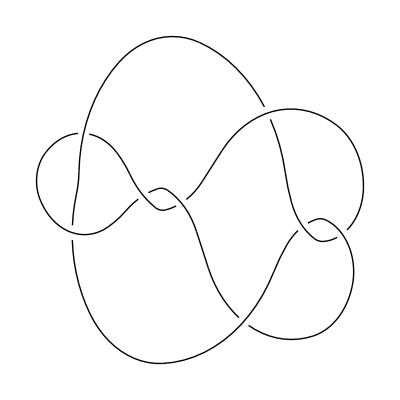

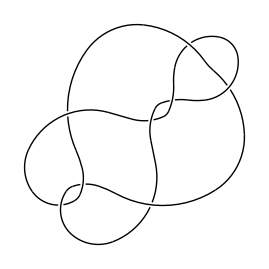

```mathematica
Show[DrawPD[PD[Knot[8,12]]]]
Show[DrawPD[PD[Mirror[Knot[8,12]]]]]
```

```mathematica
PD[Knot[8,12]]
Mirror[PD[Knot[8,12]]]
```

PD[X[4,2,5,1],X[10,8,11,7],X[8,3,9,4],X[2,9,3,10],X[14,6,15,5],X[16,11,1,12],X[12,15,13,16],X[6,14,7,13]]

PD[X[1,4,2,5],X[7,10,8,11],X[3,9,4,8],X[9,3,10,2],X[5,14,6,15],X[11,1,12,16],X[15,13,16,12],X[13,6,14,7]]